提取列表元素

Part 将取出一个列表中的某个元素。

从列表中取出第 2 个元素：

```mathematica
Part[{a,b,c,d,e,f,g},2]
```

b

[[ ... ]] 是另一种符号表示：

使用 [[2]] 来取出列表中的第 2 个元素：

```mathematica
{a,b,c,d,e,f,g}[[2]]
```

b

负数编号将从列表的末尾开始计算：

```mathematica
{a,b,c,d,e,f,g}[[-2]]
```

f

你可以通过给出一系列编号来请求提供部分列表：

取出第 2、4、5 个元素：

```mathematica
{a,b,c,d,e,f,g}[[{2,4,5}]]
```

{b,d,e}

;; 让你请求一个跨度或部分序列。

取出第 2 到 5 个元素：

```mathematica
{a,b,c,d,e,f,g}[[2;;5]]
```

{b,c,d,e}

从列表中取前 4 个元素：

```mathematica
Take[{a,b,c,d,e,f,g},4]
```

{a,b,c,d}

从一个列表中取出最后两个元素：

```mathematica
Take[{a,b,c,d,e,f,g},-2]
```

{f,g}

从列表中删除最后两个元素：

```mathematica
Drop[{a,b,c,d,e,f,g},-2]
```

{a,b,c,d,e}

现在我们来看一下列表的列表，或称数组。每个子列表就像数组中的一行。

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}//Grid
```

a | b | c
d | e | f
g | h | i

取出数组中的第二个子列表，对应于第二行：

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2]]
```

{d,e,f}

这将取出第 2 行的第 1 个元素：

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2,1]]
```

d

在数组中取出一些列也常常很有用。

通过在所有行上取出第 1 个元素，来取出第一列：

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[All,1]]
```

{a,d,g}

函数 Position 可以找到某个对象出现的位置列表。

这里只有一个 d，并且它出现在 2,1 的位置：

```mathematica
Position[{{a,b,c},{d,e,f},{g,h,i}},d]
```

{{2,1}}

这将给出 x 出现的所有位置的列表：

```mathematica
Position[{{x,y,x},{y,y,x},{x,y,y},{x,x,y}},x]
```

{{1,1},{1,3},{2,3},{3,1},{4,1},{4,2}}

“a”在一个字符列表中出现的位置：

```mathematica
Position[Characters["The Wolfram Language"],"a"]
```

{{10},{14},{18}}

找到 2^500 的各位数字中 0 出现的位置：

```mathematica
Flatten[Position[IntegerDigits[2^500],0]]
```

{7,9,19,20,44,47,50,65,75,88,89,96,103,115,116,119,120,137}

函数 ReplacePart 可以让你替换一个列表的部分内容：

将第 3 个元素替换为 x：

```mathematica
ReplacePart[{a,b,c,d,e,f,g},3->x]
```

{a,b,x,d,e,f,g}

替换两个位置：

```mathematica
ReplacePart[{a,b,c,d,e,f,g},{3->x,5->y}]
```

{a,b,x,d,y,f,g}

将 5 个随机选择的位置替换为“--”：

```mathematica
ReplacePart[Characters["The Wolfram Language"],Table[RandomInteger[{1,20}]->"--",5]]
```

{T,h,e, ,W,--,l,f,r,a,m,--,--,--,n,g,u,a,g,--}

有时，人们希望列表中的特定部分能够消失。我们可以将它们替换为 Nothing。

Nothing 会自动被删除：

```mathematica
{1,2,Nothing,4,5,Nothing}
```

{1,2,4,5}

将第 1 和第 3 个元素替换为 Nothing：

```mathematica
ReplacePart[{a,b,c,d,e,f,g},{1->Nothing,3->Nothing}]
```

{b,d,e,f,g}

随机取 50 个单词，去掉长度超过 5 个字符的单词，并将其他单词颠倒过来：

```mathematica
If[StringLength[#]>5,Nothing,StringReverse[#]]&/@RandomSample[WordList[ ],50]
```

{yllud,yciuj,poons,tsioh}

Take 将根据元素在列表中的位置来取出指定数量的元素。TakeLargest 和 TakeSmallest 是根据元素的大小来取出元素。

从列表中取出最大的 5 个元素：

```mathematica
TakeLargest[Range[20],5]
```

{20,19,18,17,16}

TakeLargestBy 和 TakeSmallestBy 是根据应用一个函数的结果来取出元素。

从前 100 个罗马数字中取出 5 个具有最大字符串长度的数字：

```mathematica
TakeLargestBy[Array[RomanNumeral,100],StringLength,5]
```

{LXXXVIII,LXXXIII,XXXVIII,LXXVIII,LXXXVII}

词汇

Part[list,n] |   | 列表的第 n 个部分
list[[n]] |   | 部分列表的缩写形式
list[[{n_1,n_2,...}]] |   | 列表的第 n_1、n_2 ... 部分
list[[n_1;;n_2]] |   | 第 n_1 到 n_2 部分的序列
list[[m,n]] |   | 数组中第 m 行第 n 列的元素
list[[All,n]] |   | 第 n 列中的所有元素
Take[list,n] |   | 取出列表中的前 n 个元素
TakeLargest[list,n] |   | 取出列表中最大的 n 个元素
TakeSmallest[list,n] |   | 取出列表中最小的 n 个元素
TakeLargestBy[list,f,n] |   | 取出应用 f 后最大的 n 个元素
TakeSmallestBy[list,f,n] |   | 取出应用 f 后最小的 n 个元素
Position[list,x] |   | 列表中 x 的所有位置
ReplacePart[list,n→x] |   | 将列表的第 n 部分替换为 x
Nothing |   | 会自动删除的列表元素

"共有 13 道习题" | "开始练习 »"

找到 2^1000 中的最后 5 位数字。»

| 期望输出： |  
  | {6,9,3,7,6} |

取出字母表中的第 10 到第 20 个字母。»

| 期望输出： |  
  | {"j","k","l","m","n","o","p","q","r","s","t"} |

将字母表中偶数位置的字母列出来。»

| 期望输出： |  
  | {"b","d","f","h","j","l","n","p","r","t","v","x","z"} |

对 12 的前 100 次方中的倒数第二位创建线条图。»

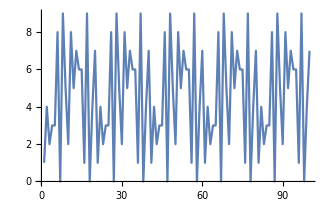
| 期望输出： |  
  | -Graphics- |

将前 20 个数字的平方和立方的列表连接起来，并取出组合的列表中最小的 10 个元素。»

| 期望输出： |  
  | {1,1,4,8,9,16,25,27,36,49} |

找到 “software” 一词在维基百科上关于 “computers” 词条中的位置。»

| 期望输出示例： |  
  | {4594,4732,4739,4747,4769,6070,6164,6186,7608,7665,7687} |

将 WordList[ ] 中的单词中字母 “e” 出现的位置创建为直方图。»

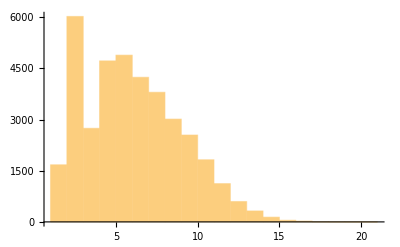
| 期望输出： |  
  | -Graphics- |

列出前 100 个数字的立方，如果立方值也是某个数字的平方，则替换为红色。»

| 期望输出： |  
  | {RGBColor[1, 0, 0],8,27,RGBColor[1, 0, 0],125,216,343,512,RGBColor[1, 0, 0],1000,1331,1728,2197,2744,3375,RGBColor[1, 0, 0],4913,5832,6859,8000,9261,10648,12167,13824,RGBColor[1, 0, 0],17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,RGBColor[1, 0, 0],50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,RGBColor[1, 0, 0],125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,RGBColor[1, 0, 0],274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,RGBColor[1, 0, 0],551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,RGBColor[1, 0, 0]} |

列出前 100 个质数，并去掉首位数小于 5 的质数。»

| 期望输出： |  
  | {5,7,53,59,61,67,71,73,79,83,89,97,503,509,521,523,541} |

创建一个从 Range[10] 开始的网格，然后在其余 9 个步骤中，每一步都随机删除一个元素。»

| 期望输出示例： |  
  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 3 | 5 | 6 | 7 | 8 | 9 | 10 |  | 
3 | 5 | 6 | 7 | 8 | 9 | 10 |  |  | 
3 | 6 | 7 | 8 | 9 | 10 |  |  |  | 
3 | 6 | 7 | 9 | 10 |  |  |  |  | 
3 | 6 | 7 | 9 |  |  |  |  |  | 
6 | 7 | 9 |  |  |  |  |  |  | 
7 | 9 |  |  |  |  |  |  |  | 
9 |  |  |  |  |  |  |  |  |  |

找出 WordList[ ] 中长度最长的 10 个单词。»

| 期望输出： |  
  | {"electroencephalographic","electroencephalograph","counterrevolutionary","buckminsterfullerene","compartmentalization","electroencephalogram","internationalization","uncharacteristically","magnetohydrodynamics","incomprehensibility"} |

找出 100 以内的整数名称中名字最长的 5 个。»

| 期望输出： |  
  | {"seventy-seven","seventy-three","seventy-eight","twenty-three","twenty-eight"} |

找出 100 以内的整数名称中 “e” 的数量最多的 5 个。»

| 期望输出： |  
  | {"seventy-three","seventeen","seventy-seven","nineteen","eleven"} |

问&答

如何读 list[[n]]？

通常是“list part n”或者“list sub n”。第二种形式(“sub”是“下标(subscript)”的缩写)来自对数学和提取向量分量的思想。

如果要求得到一个不存在的列表的一部分，会发生什么？

会得到一个消息，并且原先的计算会被退回到未完成的状态。

我可以只获得某个对象在列表中出现的第一个位置吗？

可以，使用 FirstPosition。

技术笔记

First 和 Last 等同于 [[1]] 和 [[-1]]。

在指定部分时， 1;;-1 等同于 All。

探索更多

Wolfram 语言中的列表元素指南 »